```mathematica
e=-1/2((theta_t-theta_ttilde-b)/(sigma_theta))^2-1/2((b-b_tp)/(sigma_b))^2;
Together[e];
numerator=-b^2 sigma_b^2-b^2 sigma_theta^2+2 b b_tp sigma_theta^2-b_tp^2 sigma_theta^2+2 b sigma_b^2 theta_t-sigma_b^2 theta_t^2-2 b sigma_b^2 theta_ttilde+2 sigma_b^2 theta_t theta_ttilde-sigma_b^2 theta_ttilde^2;
Collect[numerator, b]
```

-b_tp^2 (sigma:Blank[0.072])^2+b^2 (-(sigma:Blank[0.072])^2-sigma_b^2)-sigma_b^2 theta_t^2+2 sigma_b^2 theta_t theta_ttilde-sigma_b^2 theta_ttilde^2+b (2 b_tp (sigma:Blank[0.072])^2+2 sigma_b^2 theta_t-2 sigma_b^2 theta_ttilde)

```mathematica
at=.
wstilde=.
vt=.
gammaws=.
gammaa=.
atp=.
a=at*wstilde;
y=vt;
alpha=gammaws^-2+2;
k=gammaa^-2;
theta=gammaa^2atp*wstilde;
{alpha + k,((alpha-1)y^-1+theta^-1)^-1}
```

{2+1/gammaa^2+1/gammaws^2,1/((1+1/gammaws^2)/vt+1/(atp gammaa^2 wstilde))}

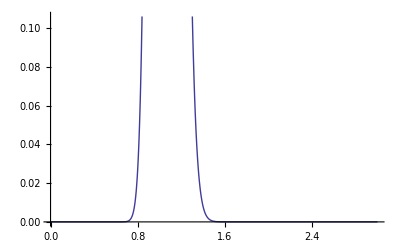

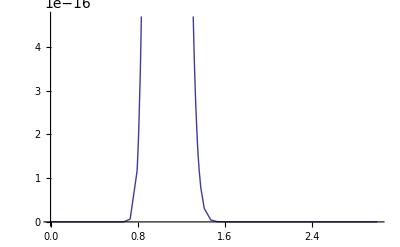

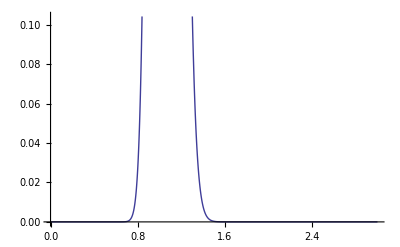

-Graphics-

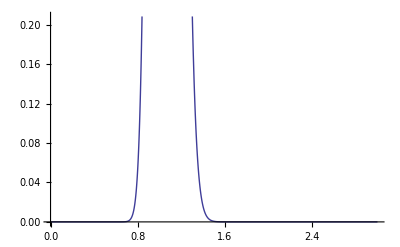

```mathematica
gammaws=0.1;
gammaa = 0.2;
atp=0.9;
vt=2.2;
wstilde=2.0;
Plot[Simplify[PDF[InverseGammaDistribution[gammaws^-2+2,(gammaws^-2+1)at*wstilde],vt]*PDF[GammaDistribution[gammaa^-2,gammaa^2*atp],at]],{at,0,3}]
Plot[a^(alpha+k-1)Exp[-a((alpha-1)y^-1+theta^-1)],{at,0,3}]
Plot[PDF[GammaDistribution[alpha+k,((alpha-1)y^-1+theta^-1)^-1],a],{at,0,3}]
Plot[PDF[GammaDistribution[gammaws^-2+gammaa^-2+2,((gammaws^-2+1)vt^-1+gammaa^-2atp^-1wstilde^-1)^-1],a],{at,0,3}]
Plot[PDF[GammaDistribution[gammaws^-2+gammaa^-2+2,((gammaws^-2+1)vt^-1wstilde+gammaa^-2atp^-1)^-1],at],{at,0,3}]
```